# Rosseller: Sections

## Rosseller System, Sensitivity, and Sections

We are going to build code and explore the behavior of the system on the standard section.

### Existing Code Fragments

#### Version 1

Right now we know how to go round a bunch of times recording stuff as we cross the Poincare section. I added the sensitivity computation.

-Graphics3D-

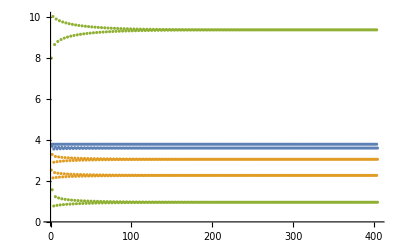

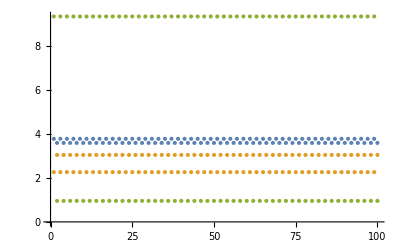

{{{3.78865,2.26831,9.36663},{{-0.363768,-4.28398,-0.356502},{0.132638,1.56202,0.129986},{-9.61282×10^-6,-0.0000235543,1.4671×10^-6}}},{{3.60131,3.0536,0.958366},{{-0.12543,-1.4772,-0.12293},{0.131688,1.55086,0.129059},{2.79438×10^-6,4.0592×10^-6,-7.65047×10^-7}}},{{3.78865,2.2683,9.36672},{{-0.363767,-4.284,-0.356504},{0.132633,1.56201,0.129987},{8.65902×10^-6,0.0000163852,-1.90835×10^-6}}},{{3.60131,3.05359,0.95834},{{-0.125436,-1.4772,-0.122927},{0.13169,1.55086,0.129058},{-3.08519×10^-6,-8.79263×10^-6,3.21116×10^-7}}}}

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
yJData=Reap[
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}
]]⟦2,1⟧;
ParametricPlot3D[ySol[t],{t, 0.9*TMax, TMax},PlotRange->All]
ListPlot[yJData⟦All,1⟧ᵀ,PlotRange->All]
ListPlot[yJData⟦-100;;-1,1⟧ᵀ,PlotRange->All]
yJData⟦-4;;-1⟧
```

#### Version 2

I can do the data extraction in a different way. If we want.

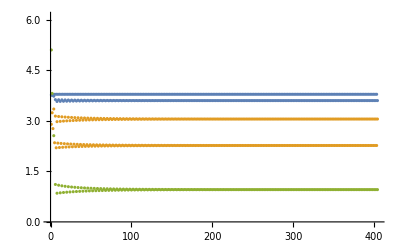

{{3.60131,3.05359,0.958342},{{1.24157,2.23782,-0.169391},{-1.30363,-2.34961,0.177864},{-0.000159545,-0.000201256,0.0000274521}}}

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={PData,{y[t],J[t]}})
}
];
PData=Partition[Flatten[PData],3+3^2];
PData=Table[yJs=PData⟦i⟧;
ys=yJs⟦1;;3⟧; Js=yJs⟦4;;3+3^2⟧;
{ys,Partition[Js,3]},{i,Length[PData]}];
yData=PData⟦All,1⟧;
ListPlot[yDataᵀ]
{yEnd, JEnd}=PData⟦-1⟧
```

```mathematica
MatrixForm[JEnd];
MatrixForm[JEndᵀ.JEnd];
MatrixForm[JEnd.JEndᵀ];
Eigenvalues[JEnd];
SingularValueList[JEnd,Tolerance->0]
```

{3.71885,0.0000506189,1.08826×10^-16}

#### Version 3

We also know how to go round once and stop the first time we cross the P-section.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=234; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={y[t],J[t]};"StopIntegration")
}
];
PData
```

{{3.77082,2.89763,5.10453},{{-0.0570967,1.85847,0.029455},{0.450972,-0.350306,-0.102516},{-3.23243,-3.22319,0.457328}}}